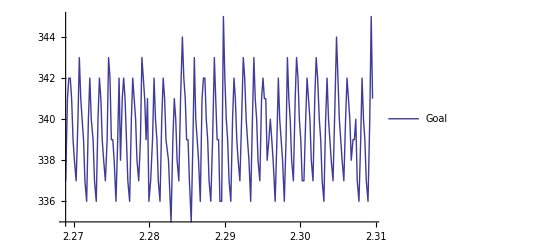

```mathematica
SetDirectory[NotebookDirectory[]];
h=400;
data=Import["data.txt","Table"];
data=data[[2;;]];
goaldata=Transpose[Transpose[data][[1;;2]]];
adcdata=Transpose[{Transpose[data][[1]],Transpose[data][[3]]}];
ListLinePlot[{(*goaldata[[1000;;1600]],*)adcdata[[1100;;1300]]},PlotRange->{All},PlotLegends->{"Goal","Value"}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -2.94537 | 0.441404 | -6.67272 | 5.35693×10^-6
o | 339.355 | 0.305667 | 1110.21 | 1.5831×10^-40
p | -4385.46 | 271.094 | -16.1769 | 2.44886×10^-11
ω | 4912.58 | 118.364 | 41.5041 | 1.01453×10^-17

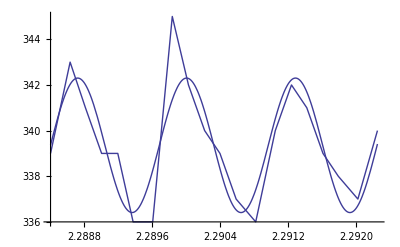

```mathematica
fitdata=adcdata[[1195;;1214]];
nlm=NonlinearModelFit[fitdata,a*Cos[t*ω+p]+o,{{a,10},o,p,{ω,3000}},t];
nlm["ParameterTable"]
Show[ListLinePlot[fitdata],Plot[nlm[t],{t,fitdata[[1]][[1]],fitdata[[-1]][[1]]}]]
```

```mathematica
ku=4/Pi*h/Abs[a]/.nlm["BestFitParameters"]
```

172.914

```mathematica
tu=2*Pi/ω/.nlm["BestFitParameters"]
```

0.001279